## Common

```mathematica
Needs["PlotLegends`"]
```

```mathematica
readRunFitness[name_]:=
Module[{allData,noHeaderData,data},
allData = ImportString[Import[name],"TSV"];
noHeaderData = Rest[allData];
data = noHeaderData⟦All,2;;⟧;
{data,noHeaderData⟦All,1⟧, Mean[Transpose[data]], Median[Transpose[data]], Min/@data}
]
```

```mathematica
readRunEvaluationInfo[name_]:=
Module[{allData,noHeaderData,data},
allData = ImportString[Import[name],"TSV"];
data = Rest[allData];
{data,Max/@data, Mean[Transpose[data]], Median[Transpose[data]], Min/@data}
]
```

```mathematica
enlarge[list_, fill_, stat_]:=list~Join~Array[fill&,Max[Length/@stat]-Length[list]]
```

```mathematica
enlarge[list_, fill_, stat_, len_]:=list~Join~Array[fill&,len-Length[list]]
```

This function reads single stat for all experiment runs by multiple parameters/methods. Typical use for "experiments_???.txt" file.

```mathematica
readFinalStats[names_List,statName_]:=
Module[{allData},
allData = ImportString[Import[#],"TSV"]&/@names;
allData⟦#⟦1⟧,2;;,#⟦3⟧⟧&/@Position[allData,statName]
]
```

Reads all stat names from multiple parameters/methods. Returns their intersection.

```mathematica
readFinalStatNames[names_List]:=
Module[{allData},
Flatten[Intersection[(ImportString[Import[#],"TSV"]&/@names)⟦All,1,All⟧]]
]
```

```mathematica
listAllExperimentFiles[dirs_List]:=
Flatten[FileNames[RegularExpression["experiments\\_\\d\\d\\d\\.txt"],{"/Users/drchaj1/java/exp/"<>#}]&/@dirs]
```

```mathematica
listAllParameterFiles[dirs_List]:=
Flatten[FileNames[RegularExpression["parameters\\_\\d\\d\\d\\.txt"],{"/Users/drchaj1/java/exp/"<>#}]&/@dirs]
```

Show table showing success of each method (config), the same as a bar chart and then box-plots for all stats. Give a stat name to sort by and a number of different configuration to assign different colors.

```mathematica
finalStatsAll[listOfFiles_,methodNames_,sortBy_:Null,numOfConfs_:1]:=
Module[{files,methods,statNames,statPosition,data,order,labels,labelPlacement,success,colors},
(* Permutate files and labels *)
files=Flatten[Transpose[Partition[listOfFiles,Length[listOfFiles]/numOfConfs]]];
methods=Flatten[Transpose[Partition[methodNames,Length[methodNames]/numOfConfs]]];

(* Names of all stats. *)
statNames=readFinalStatNames[files];
(* A position of a stat to sort by. *)
statPosition=Flatten[Position[statNames,sortBy]];
data=readFinalStats[files,#]&/@statNames;
(* Now sort-by stat given or not existing one given. *)
If[Length[statPosition]==1,
order=Ordering[Median/@data[[statPosition⟦1⟧]]],
order=Range[Length[files]]
];
(* Sort data and labels. *)
data=Part[#,order]&/@data;
labels =methods⟦order⟧;

(* Compute % of sucessful runs *) 
success=N[100*Count[#,"true"]/Length[#]&/@data⟦Sequence@@Flatten[Position[statNames,"SUCCESS"]]⟧];

(* Prepare colors *)
If[numOfConfs==1,
colors="Rainbow",
colors=Take[ColorData[10,"ColorList"],numOfConfs]
(*colors=Take[{LightRed,LightGreen,LightBlue,LightOrange,LightBrown,LightCyan,LightMagenta},numOfConfs]*)
];

(* Print them as a table. *)
Print[Grid[Transpose@{{Style["ID",Bold]}~Join~labels,{Style["SUCCESS %",Bold]}~Join~success,{Style["DIR",Bold]}~Join~(StringReplace[#,"/Users/drchaj1/java/exp/"->""]&/@files)},Frame->All]];
(* And a bar chart. *)
labelPlacement=Placed[Style[#,FontSize->15]&/@labels,Axis,Rotate[#,Pi/2]&];
Print[BarChart[success,ChartLabels->labelPlacement,ChartStyle->colors,LabelingFunction->Center,ImageSize->1200]];
(* All other stats as box plots.*)
Grid[Transpose[{statNames,
BoxWhiskerChart[#,"Notched",ChartLabels->labelPlacement,ChartStyle->colors,ImageSize->1200]&
/@data
}]]
]
```

Performs two-tailed Mann-Whitney-Wilcoxon test on two given experiment files and the name of a stat. This non-parametric test compares whether two independent samples of observations have equally large values. Test homoscedasticity, see Steve McKillup: Statistics Explained, An Introductory Guide for Life Scientists,  p. 224 and  p. 152.

```mathematica
testMannWhitney[file1_,file2_,statName_]:=
Module[{data1,data2,vars,res},
data1=Flatten[readFinalStats[{"/Users/drchaj1/java/exp/"<>file1},statName]];
data2=Flatten[readFinalStats[{"/Users/drchaj1/java/exp/"<>file2},statName]];
vars={Variance[data1],Variance[data2]};
Print["median 1: ",Median[data1]];
Print["median 2: ",Median[data2]];
Print["mean 1: ",Mean[data1]];
Print["mean 2: ",Mean[data2]];
Print["variance 1: ",vars⟦1⟧];
Print["variance 2: ",vars⟦2⟧];
vars=Sort[vars];
Print["higher/lower variance ratio: ",vars⟦2⟧/vars⟦1⟧];
If[vars⟦2⟧/vars⟦1⟧>4,Print["WARNING: ratio > 4"]];
res=MannWhitneyTest[{data1,data2},Automatic,"HypothesisTestData"];
Print["U stat: ", res["TestData"]⟦1⟧];
Print["P-value: ", res["TestData"]⟦2⟧];
Print[res["TestConclusion"]];
]
```

Gives a list of parameter files sorted according to paramOrder. The paramOrder is  a list of changing parameters (at the end of the parameter file). Function returns a sorted list of items in form: {parameter file, {values of parameters in order paramOrder, ...}}.

```mathematica
sortExperimentDirs[dirs_List,paramOrder_]:=
Module[{parameterFiles,matchedLines,extractedkeys,
(* This converts string to expression, but keeps complex numbers as strings (solves problem with "I" input.).*)
comparableExpression:=Function[x,If[NumberQ[ToExpression[x]]&&UnsameQ[Head[ToExpression[x]],Complex],ToExpression[x],x]]
},
(* All para files. *)
parameterFiles=listAllParameterFiles[dirs];
(* Take a last occurence of each parameter selected to sort for each parameter file. *)
matchedLines=Outer[StringTrim[Last[FindList[#1,#2]],#2<>" = "]&,parameterFiles,paramOrder];
(* Get sorted list of items in form: {parameter file, {values of parameters in order paramOrder, ...}}. *)
Sort[MapThread[{#1,#2}&,{parameterFiles,matchedLines}],OrderedQ[{comparableExpression/@#1⟦2⟧,comparableExpression/@#2⟦2⟧}]&]
]
```

Uses the previous function to create a new experiment directory with sorted experiments.

```mathematica
sortExperimentDirsToANew[dirs_List,paramOrder_,targetDir_]:=
Module[{sortedDirs,fullTargetDir},
sortedDirs=sortExperimentDirs[dirs,paramOrder];
Print[Grid[Transpose@{
{Style["ID",Bold]}~Join~Range[Length[sortedDirs]],
{Style["PARAM FILE",Bold]}~Join~(StringReplace[#,"/Users/drchaj1/java/exp/"->""]&/@sortedDirs⟦All,1⟧),
{Style["PARAMS",Bold]}~Join~sortedDirs⟦All,2⟧
},Frame->All]];
(* Create target directory. *)
fullTargetDir="/Users/drchaj1/java/exp/"<>targetDir;
CreateDirectory[fullTargetDir,CreateIntermediateDirectories->True];
(* Copy parameter files. *)
MapIndexed[
CopyFile[
#1,
FileNameJoin[{fullTargetDir,"parameters_"<>ToString[PaddedForm[#2⟦1⟧,2,NumberPadding->{"0","0"}]]<>".txt"}]
]&,
sortedDirs⟦All,1⟧];
(* Copy experiment files. *)
MapIndexed[
CopyFile[
StringReplace[#1,"parameters"->"experiments"],
FileNameJoin[{fullTargetDir,"experiments_"<>ToString[PaddedForm[#2⟦1⟧,2,NumberPadding->{"0","0"}]]<>".txt"}]
]&,
sortedDirs⟦All,1⟧];
]
```

## Fitness of a Single Run

```mathematica
{data, bsf, avg, med, min}=readRunFitness["~/java/exp/results/run_001_001_FITNESS.txt"];
```

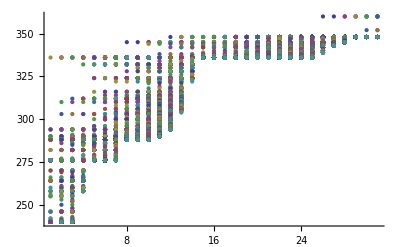

```mathematica
ListPlot[Transpose[data], PlotRange->All]
```

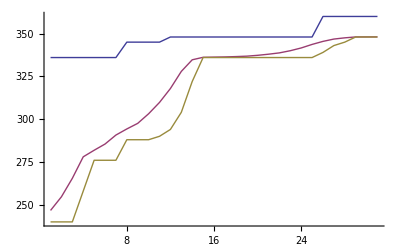

```mathematica
ListLinePlot[{bsf, avg, min}, PlotRange->All]
```

## Fitness over Multiple Runs

```mathematica
bsfAvg = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/results"}]);
```

```mathematica
Max[Length[#]&/@bsfAvg]
```

161

```mathematica
enlarge[list_]:=list~Join~Array[Max[bsfAvg]&,Max[Length/@bsfAvg]-Length[list]]
```

```mathematica
bsfAvg=Mean[(enlarge/@bsfAvg)];
```

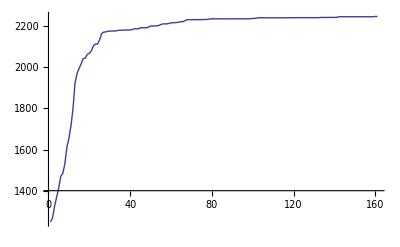

```mathematica
ListLinePlot[{bsfAvg}, PlotRange->All]
```

## Evaluation of a Single Run

```mathematica
{data, max, avg, med, min}=readRunEvaluationInfo["~/java/exp/results/run_001_001_AVG_DISTANCE.txt"];
```

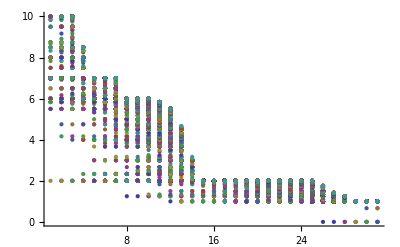

```mathematica
ListPlot[Transpose[data], PlotRange->All]
```

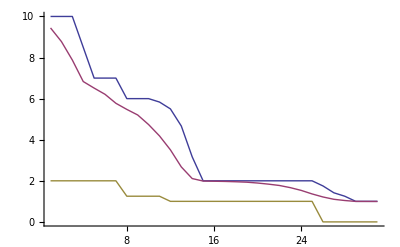

```mathematica
ListLinePlot[{max, avg, min}, PlotRange->All]
```

## Evaluation over Multiple Runs

```mathematica
bsfAvg = (readRunEvaluationInfo[#]⟦5⟧&/@FileNames["run_001*AVG_DISTANCE.txt",{"~/java/exp/results"}]);
```

```mathematica
Max[Length[#]&/@bsfAvg]
```

161

```mathematica
bsfAvg=Mean[enlarge[#,Min[bsfAvg], bsfAvg]&/@bsfAvg];
```

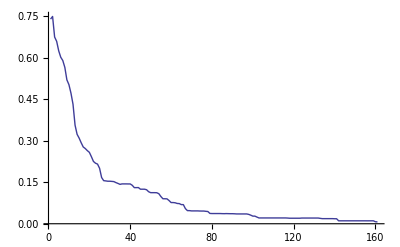

```mathematica
ListLinePlot[{bsfAvg}, PlotRange->All]
```

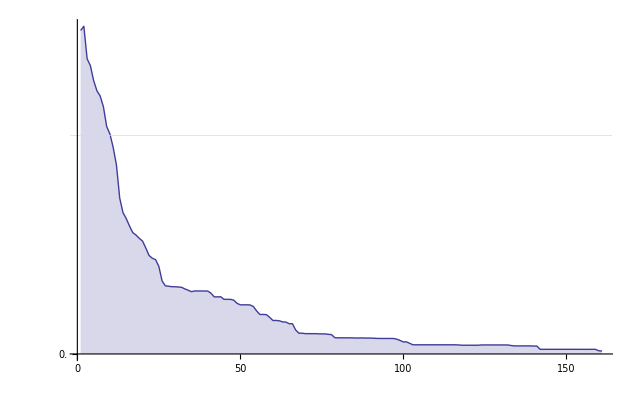

```mathematica
Show[ListLinePlot[{bsfAvg[[1;;]]}, PlotRange->All, Ticks->{Range[0,300, 50],Range[0,25, 0.5]},Filling->Axis,AxesOrigin->{0,0}], GridLines->{None, {0.5}}]
```

## Evaluation over Multiple Methods

```mathematica
singleMethod[methodDir_, variable_, column_] :=
Module[{stat},
stat=(readRunFitness[#]⟦column⟧&/@(Complement[FileNames["run_001*"<>variable<>".txt",{"~/java/exp/results/"<>methodDir}],FileNames["run_001*GENERALIZATION*.txt",{"~/java/exp/results/"<>methodDir}]]));
Mean[enlarge[#,Max[#], stat]&/@stat]
]
```

```mathematica
singleMethodGeneralization[methodDir_, variable_] :=
Module[{stat},
stat = Sequence@@Flatten[#,{3}]&@(ImportString[Import[#],"TSV"]&/@
Intersection[FileNames["run_001*"<>variable<>".txt",{"~/java/exp/results/"<>methodDir}],FileNames["run_001*GENERALIZATION*.txt",{"~/java/exp/results/"<>methodDir}]]);
Mean[enlarge[#,Min[#], stat]&/@stat]
]
```

```mathematica
singleMethodDiversity[methodDir_, variable_] :=
Module[{stat},
stat = Sequence@@Flatten[#,{3}]&@(ImportString[Import[#],"TSV"]&/@
FileNames["run_001_*"<>variable<>"*.txt",{"~/java/exp/results/"<>methodDir}]);
Rescale[Mean[enlarge[#,Mean[#], stat]&/@stat]];
Mean[enlarge[#,Mean[#], stat]&/@stat]
]
```

```mathematica
multipleMethods[methodDirs_, variable_, column_, generalization_:True] :=
Module[{stats, len},
If[generalization==True,
stats=(singleMethod[#,variable, column]&/@methodDirs)~Join~(singleMethodGeneralization[#,variable]&/@methodDirs),
stats=(singleMethod[#,variable, column]&/@methodDirs)];
len = Max[Length/@stats];
stats=enlarge[#,Min[#], stats, len]&/@stats;
Show[
ListLinePlot[stats, PlotRange->All, Ticks->{Range[0,300, 50],Range[0,25, 0.5]},AxesOrigin->{0,0}, PlotStyle->{Thickness[0.005]},
PlotLegend->methodDirs~Join~(StringJoin[#," G"]&/@methodDirs),
PlotMarkers->Automatic,
LegendPosition->{1.1,-0.4}
], 
GridLines->{None, {0.5}}]
]
```

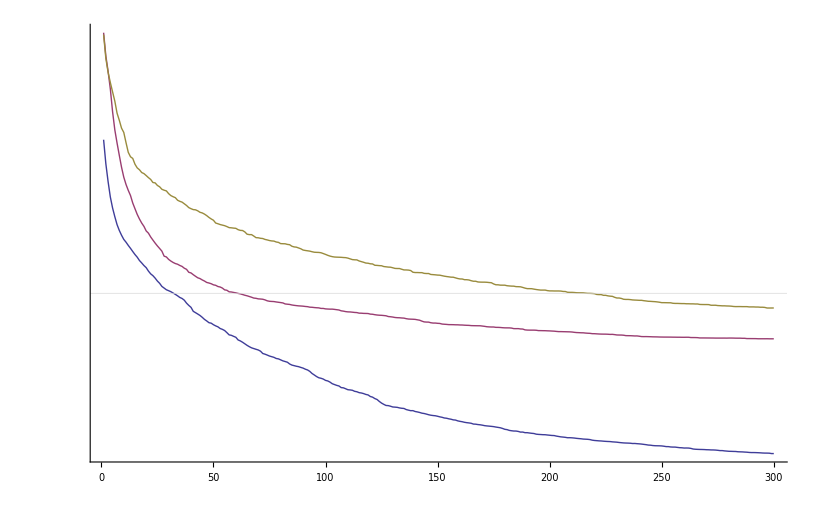

```mathematica
multipleMethods[{"FC_NEAT", "FC_GP", "FC_GPDC"}, "AVG_DISTANCE", 5]
```

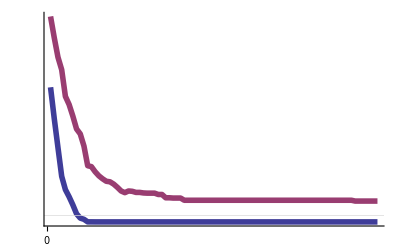

```mathematica
multipleMethods[{"T_NEAT", "T_GP"}, "AVG_DISTANCE", 5]
```

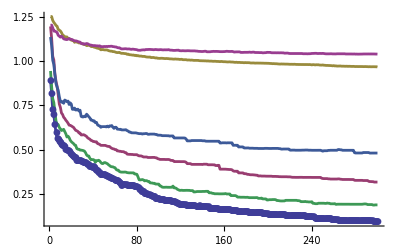

```mathematica
multipleMethods[{"FC_NEAT_7_20", "FC_GP_7_20", "FC_SADE_7_20"}, "AVG_DISTANCE", 5]
```

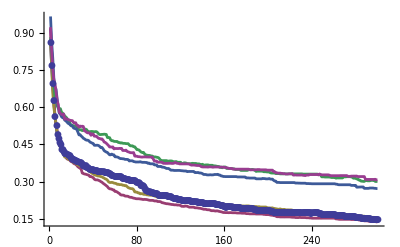

```mathematica
multipleMethods[{"DIV_GP_5_50", "DIV_NEAT_5_50", "DIV_NEAT_5_50_AMP10"}, "AVG_DISTANCE", 5]
```

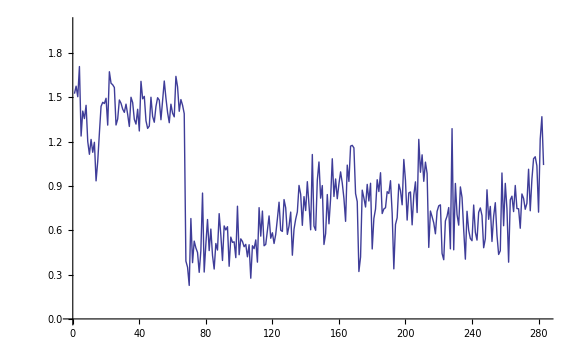

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_GP_5_50"},"DIVERSITY"],PlotRange->{0,2}]
```

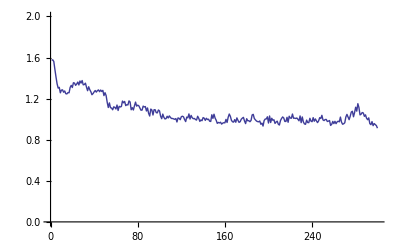

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_NEAT_5_50"},"DIVERSITY"],PlotRange->{0,2}]
```

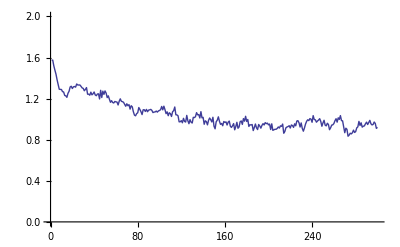

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_NEAT_5_50_AMP10"},"DIVERSITY"],PlotRange->{0,2}]
```

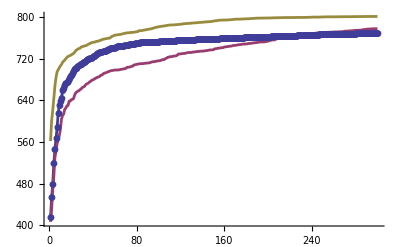

```mathematica
multipleMethods[{"DIV_GP_7_50","DIV_GPC_7_50", "DIV_NEAT_7_50"}, "FITNESS", 2, False]
```

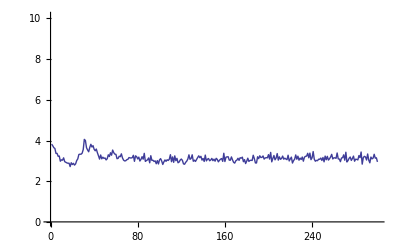

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_GP_7_50"},"P_DIVERSITY"],PlotRange->{0,10.1}]
```

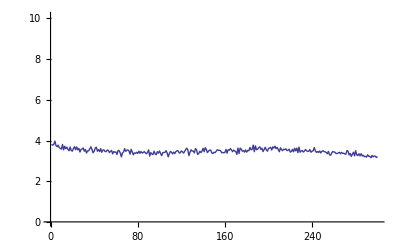

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_GPC_7_50"},"P_DIVERSITY"],PlotRange->{0,10.1}]
```

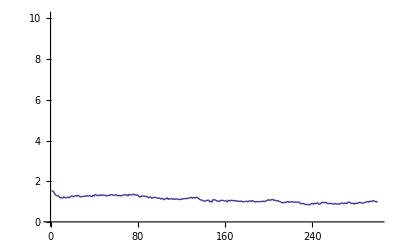

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_NEAT_7_50"},"P_DIVERSITY"],PlotRange->{0,10.1}]
```

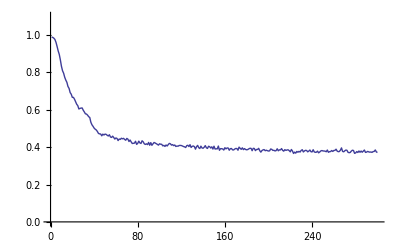

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_GP_7_50"},"G_DIVERSITY"],PlotRange->{0,1.1}]
```

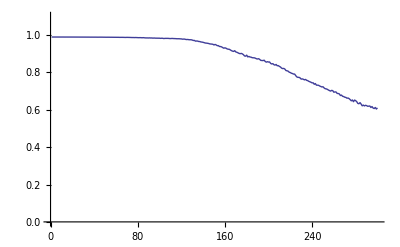

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_GPC_7_50"},"G_DIVERSITY"],PlotRange->{0,1.1}]
```

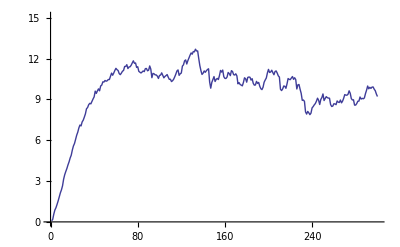

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_NEAT_7_50"},"G_DIVERSITY"],PlotRange->{0,15.1}]
```

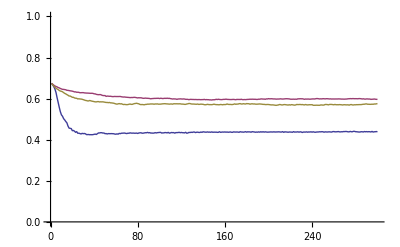

```mathematica
ListLinePlot[{singleMethodDiversity[{"GEP_TOURNAMENT"},"G_DIVERSITY"], singleMethodDiversity[{"GEP_ROULETTE"},"G_DIVERSITY"], singleMethodDiversity[{"GEP_TOURNAMENT2"},"G_DIVERSITY"]},PlotRange->{0,1}]
```

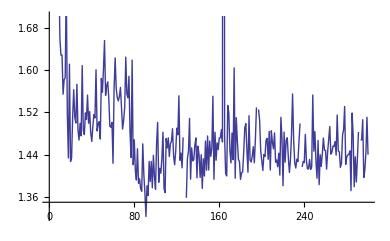

```mathematica
ListLinePlot[{singleMethodDiversity[{"GEP_TOURNAMENT"},"P_DIVERSITY"]}]
```

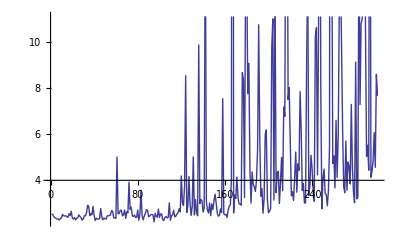

```mathematica
ListLinePlot[{singleMethodDiversity[{"GEP_TOURNAMENT2"},"P_DIVERSITY"]}]
```

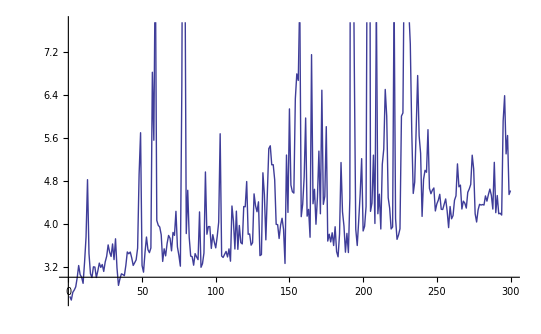

```mathematica
ListLinePlot[{singleMethodDiversity[{"GEP_ROULETTE"},"P_DIVERSITY"]}]
```

## Final Stats

```mathematica
sortExperimentDirsToANew[{"GPAT4D_SSM_500_5","GPAT4D_SSM_500_REST_A_B_S4_7","GPAT4D_SSM_500_REST_A_B_S10_20","GPAT4D_SSM_500_REST_E","GPAT4D_SSM_500_REST_G_I"},{"GPAT.SPECIES_SIZE_MEAN","SYMBOLIC_REGRESSION_4D.F"},"GPAT4D_SSM_500_S4-20"]
```

ID | PARAM FILE | PARAMS
1 | GPAT4D_SSM_500_REST_A_B_S4_7/parameters_001.txt | {4.0,A}
2 | GPAT4D_SSM_500_REST_A_B_S4_7/parameters_002.txt | {4.0,B}
3 | GPAT4D_SSM_500_5/parameters_001.txt | {4.0,C}
4 | GPAT4D_SSM_500_5/parameters_002.txt | {4.0,D}
5 | GPAT4D_SSM_500_REST_E/parameters_001.txt | {4.0,E}
6 | GPAT4D_SSM_500_5/parameters_003.txt | {4.0,F}
7 | GPAT4D_SSM_500_REST_G_I/parameters_001.txt | {4.0,G}
8 | GPAT4D_SSM_500_5/parameters_004.txt | {4.0,H}
9 | GPAT4D_SSM_500_REST_G_I/parameters_002.txt | {4.0,I}
10 | GPAT4D_SSM_500_5/parameters_005.txt | {4.0,ZFC55}
11 | GPAT4D_SSM_500_REST_A_B_S4_7/parameters_006.txt | {7.0,A}
12 | GPAT4D_SSM_500_REST_A_B_S4_7/parameters_007.txt | {7.0,B}
13 | GPAT4D_SSM_500_5/parameters_006.txt | {7.0,C}
14 | GPAT4D_SSM_500_5/parameters_007.txt | {7.0,D}
15 | GPAT4D_SSM_500_REST_E/parameters_002.txt | {7.0,E}
16 | GPAT4D_SSM_500_5/parameters_008.txt | {7.0,F}
17 | GPAT4D_SSM_500_REST_G_I/parameters_003.txt | {7.0,G}
18 | GPAT4D_SSM_500_5/parameters_009.txt | {7.0,H}
19 | GPAT4D_SSM_500_REST_G_I/parameters_004.txt | {7.0,I}
20 | GPAT4D_SSM_500_5/parameters_010.txt | {7.0,ZFC55}
21 | GPAT4D_SSM_500_REST_A_B_S10_20/parameters_001.txt | {10.0,A}
22 | GPAT4D_SSM_500_REST_A_B_S10_20/parameters_002.txt | {10.0,B}
23 | GPAT4D_SSM_500_5/parameters_011.txt | {10.0,C}
24 | GPAT4D_SSM_500_5/parameters_012.txt | {10.0,D}
25 | GPAT4D_SSM_500_REST_E/parameters_003.txt | {10.0,E}
26 | GPAT4D_SSM_500_5/parameters_013.txt | {10.0,F}
27 | GPAT4D_SSM_500_REST_G_I/parameters_005.txt | {10.0,G}
28 | GPAT4D_SSM_500_5/parameters_014.txt | {10.0,H}
29 | GPAT4D_SSM_500_REST_G_I/parameters_006.txt | {10.0,I}
30 | GPAT4D_SSM_500_5/parameters_015.txt | {10.0,ZFC55}
31 | GPAT4D_SSM_500_REST_A_B_S10_20/parameters_003.txt | {20.0,A}
32 | GPAT4D_SSM_500_REST_A_B_S10_20/parameters_004.txt | {20.0,B}
33 | GPAT4D_SSM_500_5/parameters_016.txt | {20.0,C}
34 | GPAT4D_SSM_500_5/parameters_017.txt | {20.0,D}
35 | GPAT4D_SSM_500_REST_E/parameters_004.txt | {20.0,E}
36 | GPAT4D_SSM_500_5/parameters_018.txt | {20.0,F}
37 | GPAT4D_SSM_500_REST_G_I/parameters_007.txt | {20.0,G}
38 | GPAT4D_SSM_500_5/parameters_019.txt | {20.0,H}
39 | GPAT4D_SSM_500_REST_G_I/parameters_008.txt | {20.0,I}
40 | GPAT4D_SSM_500_5/parameters_020.txt | {20.0,ZFC55}

```mathematica
labels=Flatten[Outer[StringJoin,{"GP_","70_","33_","53_","35_","55_"},{"A","B","C","D","E","F","G"}]]
```

{GP_A,GP_B,GP_C,GP_D,GP_E,GP_F,GP_G,70_A,70_B,70_C,70_D,70_E,70_F,70_G,33_A,33_B,33_C,33_D,33_E,33_F,33_G,53_A,53_B,53_C,53_D,53_E,53_F,53_G,35_A,35_B,35_C,35_D,35_E,35_F,35_G,55_A,55_B,55_C,55_D,55_E,55_F,55_G}

```mathematica
labels=Flatten[Outer[StringJoin,{"GP_","S4_","S7_","S10_","S20_"},{"A","B","C","D","E","F","G","H","I","J","K"}]]
```

{GP_A,GP_B,GP_C,GP_D,GP_E,GP_F,GP_G,GP_H,GP_I,GP_J,GP_K,S4_A,S4_B,S4_C,S4_D,S4_E,S4_F,S4_G,S4_H,S4_I,S4_J,S4_K,S7_A,S7_B,S7_C,S7_D,S7_E,S7_F,S7_G,S7_H,S7_I,S7_J,S7_K,S10_A,S10_B,S10_C,S10_D,S10_E,S10_F,S10_G,S10_H,S10_I,S10_J,S10_K,S20_A,S20_B,S20_C,S20_D,S20_E,S20_F,S20_G,S20_H,S20_I,S20_J,S20_K}

```mathematica
labels=Flatten[Outer[StringJoin,{"GP_","S4_","S7_","S10_","S20_","S33_","S50_"},{"A","B","C","D","E","F","G","H","I","FC55"}]]
```

{GP_A,GP_B,GP_C,GP_D,GP_E,GP_F,GP_G,GP_H,GP_I,GP_FC55,S4_A,S4_B,S4_C,S4_D,S4_E,S4_F,S4_G,S4_H,S4_I,S4_FC55,S7_A,S7_B,S7_C,S7_D,S7_E,S7_F,S7_G,S7_H,S7_I,S7_FC55,S10_A,S10_B,S10_C,S10_D,S10_E,S10_F,S10_G,S10_H,S10_I,S10_FC55,S20_A,S20_B,S20_C,S20_D,S20_E,S20_F,S20_G,S20_H,S20_I,S20_FC55,S33_A,S33_B,S33_C,S33_D,S33_E,S33_F,S33_G,S33_H,S33_I,S33_FC55,S50_A,S50_B,S50_C,S50_D,S50_E,S50_F,S50_G,S50_H,S50_I,S50_FC55}

```mathematica
files= listAllExperimentFiles[{"GP4D_1000","GPAT4D_SL_70_1000","GPAT4D_SL_1000"}];
```

```mathematica
files= listAllExperimentFiles[{"20110803/GP3D_1000","GPAT3D_SSM_500_S4-20"}]
```

{/Users/drchaj1/java/exp/20110803/GP3D_1000/experiments_001.txt,/Users/drchaj1/java/exp/20110803/GP3D_1000/experiments_002.txt,/Users/drchaj1/java/exp/20110803/GP3D_1000/experiments_003.txt,/Users/drchaj1/java/exp/20110803/GP3D_1000/experiments_004.txt,/Users/drchaj1/java/exp/20110803/GP3D_1000/experiments_005.txt,/Users/drchaj1/java/exp/20110803/GP3D_1000/experiments_006.txt,/Users/drchaj1/java/exp/20110803/GP3D_1000/experiments_007.txt,/Users/drchaj1/java/exp/20110803/GP3D_1000/experiments_008.txt,/Users/drchaj1/java/exp/20110803/GP3D_1000/experiments_009.txt,/Users/drchaj1/java/exp/20110803/GP3D_1000/experiments_010.txt,/Users/drchaj1/java/exp/20110803/GP3D_1000/experiments_011.txt,/Users/drchaj1/java/exp/GPAT3D_SSM_500_S4-20/experiments_001.txt,/Users/drchaj1/java/exp/GPAT3D_SSM_500_S4-20/experiments_002.txt,/Users/drchaj1/java/exp/GPAT3D_SSM_500_S4-20/experiments_003.txt,/Users/drchaj1/java/exp/GPAT3D_SSM_500_S4-20/experiments_004.txt,/Users/drchaj1/java/exp/GPAT3D_SSM_500_S4-20/experiments_005.txt,/Users/drchaj1/java/exp/GPAT3D_SSM_500_S4-20/experiments_006.txt,/Users/drchaj1/java/exp/GPAT3D_SSM_500_S4-20/experiments_007.txt,/Users/drchaj1/java/exp/GPAT3D_SSM_500_S4-20/experiments_008.txt,/Users/drchaj1/java/exp/GPAT3D_SSM_500_S4-20/experiments_009.txt,/Users/drchaj1/java/exp/GPAT3D_SSM_500_S4-20/experiments_010.txt,/Users/drchaj1/java/exp/GPAT3D_SSM_500_S4-20/experiments_011.txt,/Users/drchaj1/java/exp/GPAT3D_SSM_500_S4-20/experiments_012.txt,/Users/drchaj1/java/exp/GPAT3D_SSM_500_S4-20/experiments_013.txt,/Users/drchaj1/java/exp/GPAT3D_SSM_500_S4-20/experiments_014.txt,/Users/drchaj1/java/exp/GPAT3D_SSM_500_S4-20/experiments_015.txt,/Users/drchaj1/java/exp/GPAT3D_SSM_500_S4-20/experiments_016.txt,/Users/drchaj1/java/exp/GPAT3D_SSM_500_S4-20/experiments_017.txt,/Users/drchaj1/java/exp/GPAT3D_SSM_500_S4-20/experiments_018.txt,/Users/drchaj1/java/exp/GPAT3D_SSM_500_S4-20/experiments_019.txt,/Users/drchaj1/java/exp/GPAT3D_SSM_500_S4-20/experiments_020.txt,/Users/drchaj1/java/exp/GPAT3D_SSM_500_S4-20/experiments_021.txt,/Users/drchaj1/java/exp/GPAT3D_SSM_500_S4-20/experiments_022.txt,/Users/drchaj1/java/exp/GPAT3D_SSM_500_S4-20/experiments_023.txt,/Users/drchaj1/java/exp/GPAT3D_SSM_500_S4-20/experiments_024.txt,/Users/drchaj1/java/exp/GPAT3D_SSM_500_S4-20/experiments_025.txt,/Users/drchaj1/java/exp/GPAT3D_SSM_500_S4-20/experiments_026.txt,/Users/drchaj1/java/exp/GPAT3D_SSM_500_S4-20/experiments_027.txt,/Users/drchaj1/java/exp/GPAT3D_SSM_500_S4-20/experiments_028.txt,/Users/drchaj1/java/exp/GPAT3D_SSM_500_S4-20/experiments_029.txt,/Users/drchaj1/java/exp/GPAT3D_SSM_500_S4-20/experiments_030.txt,/Users/drchaj1/java/exp/GPAT3D_SSM_500_S4-20/experiments_031.txt,/Users/drchaj1/java/exp/GPAT3D_SSM_500_S4-20/experiments_032.txt,/Users/drchaj1/java/exp/GPAT3D_SSM_500_S4-20/experiments_033.txt,/Users/drchaj1/java/exp/GPAT3D_SSM_500_S4-20/experiments_034.txt,/Users/drchaj1/java/exp/GPAT3D_SSM_500_S4-20/experiments_035.txt,/Users/drchaj1/java/exp/GPAT3D_SSM_500_S4-20/experiments_036.txt,/Users/drchaj1/java/exp/GPAT3D_SSM_500_S4-20/experiments_037.txt,/Users/drchaj1/java/exp/GPAT3D_SSM_500_S4-20/experiments_038.txt,/Users/drchaj1/java/exp/GPAT3D_SSM_500_S4-20/experiments_039.txt,/Users/drchaj1/java/exp/GPAT3D_SSM_500_S4-20/experiments_040.txt,/Users/drchaj1/java/exp/GPAT3D_SSM_500_S4-20/experiments_041.txt,/Users/drchaj1/java/exp/GPAT3D_SSM_500_S4-20/experiments_042.txt,/Users/drchaj1/java/exp/GPAT3D_SSM_500_S4-20/experiments_043.txt,/Users/drchaj1/java/exp/GPAT3D_SSM_500_S4-20/experiments_044.txt}

```mathematica
labels=Range[Length[files]];
```

```mathematica
testMannWhitney["GPAT1D_SL_1000/experiments_001.txt","GPAT1D_SL_1000/experiments_015.txt","ARITY_BSF"]
```

median 1: 1.

median 2: 1.

mean 1: 1.013

mean 2: 1.014

variance 1: 0.0128438

variance 2: 0.0138178

higher/lower variance ratio: 1.07583

U stat: 499500

P-value: 0.964538

The null hypothesis that the median difference is 0 is not rejected at the 5. percent level based on the Mann-Whitney test.

ID | SUCCESS % | DIR
GP_A | 95.7 | 20110803/GP3D_1000/experiments_001.txt
S4_A | 99.8 | GPAT3D_SSM_500_S4-20/experiments_001.txt
S7_A | 99.6 | GPAT3D_SSM_500_S4-20/experiments_012.txt
S10_A | 99.6 | GPAT3D_SSM_500_S4-20/experiments_023.txt
S20_A | 99.8 | GPAT3D_SSM_500_S4-20/experiments_034.txt
GP_B | 71.1 | 20110803/GP3D_1000/experiments_002.txt
S4_B | 85.8 | GPAT3D_SSM_500_S4-20/experiments_002.txt
S7_B | 89.6 | GPAT3D_SSM_500_S4-20/experiments_013.txt
S10_B | 92.4 | GPAT3D_SSM_500_S4-20/experiments_024.txt
S20_B | 90. | GPAT3D_SSM_500_S4-20/experiments_035.txt
GP_C | 76.2 | 20110803/GP3D_1000/experiments_003.txt
S4_C | 99.2 | GPAT3D_SSM_500_S4-20/experiments_003.txt
S7_C | 100. | GPAT3D_SSM_500_S4-20/experiments_014.txt
S10_C | 100. | GPAT3D_SSM_500_S4-20/experiments_025.txt
S20_C | 100. | GPAT3D_SSM_500_S4-20/experiments_036.txt
GP_D | 32.6 | 20110803/GP3D_1000/experiments_004.txt
S4_D | 89.8 | GPAT3D_SSM_500_S4-20/experiments_004.txt
S7_D | 92.4 | GPAT3D_SSM_500_S4-20/experiments_015.txt
S10_D | 93.8 | GPAT3D_SSM_500_S4-20/experiments_026.txt
S20_D | 96. | GPAT3D_SSM_500_S4-20/experiments_037.txt
GP_E | 27.6 | 20110803/GP3D_1000/experiments_005.txt
S4_E | 31.8 | GPAT3D_SSM_500_S4-20/experiments_005.txt
S7_E | 41.4 | GPAT3D_SSM_500_S4-20/experiments_016.txt
S10_E | 48.6 | GPAT3D_SSM_500_S4-20/experiments_027.txt
S20_E | 63.6 | GPAT3D_SSM_500_S4-20/experiments_038.txt
GP_F | 29.1 | 20110803/GP3D_1000/experiments_006.txt
S4_F | 91.2 | GPAT3D_SSM_500_S4-20/experiments_006.txt
S7_F | 93. | GPAT3D_SSM_500_S4-20/experiments_017.txt
S10_F | 95.8 | GPAT3D_SSM_500_S4-20/experiments_028.txt
S20_F | 98.2 | GPAT3D_SSM_500_S4-20/experiments_039.txt
GP_G | 13.4 | 20110803/GP3D_1000/experiments_007.txt
S4_G | 72.4 | GPAT3D_SSM_500_S4-20/experiments_007.txt
S7_G | 78.8 | GPAT3D_SSM_500_S4-20/experiments_018.txt
S10_G | 82. | GPAT3D_SSM_500_S4-20/experiments_029.txt
S20_G | 83.8 | GPAT3D_SSM_500_S4-20/experiments_040.txt
GP_H | 7.5 | 20110803/GP3D_1000/experiments_008.txt
S4_H | 24. | GPAT3D_SSM_500_S4-20/experiments_008.txt
S7_H | 47.6 | GPAT3D_SSM_500_S4-20/experiments_019.txt
S10_H | 58.6 | GPAT3D_SSM_500_S4-20/experiments_030.txt
S20_H | 63.8 | GPAT3D_SSM_500_S4-20/experiments_041.txt
GP_I | 9.6 | 20110803/GP3D_1000/experiments_009.txt
S4_I | 0.4 | GPAT3D_SSM_500_S4-20/experiments_009.txt
S7_I | 1. | GPAT3D_SSM_500_S4-20/experiments_020.txt
S10_I | 0.6 | GPAT3D_SSM_500_S4-20/experiments_031.txt
S20_I | 1.4 | GPAT3D_SSM_500_S4-20/experiments_042.txt
GP_J | 47.5 | 20110803/GP3D_1000/experiments_010.txt
S4_J | 1.2 | GPAT3D_SSM_500_S4-20/experiments_010.txt
S7_J | 2.6 | GPAT3D_SSM_500_S4-20/experiments_021.txt
S10_J | 2.8 | GPAT3D_SSM_500_S4-20/experiments_032.txt
S20_J | 4.6 | GPAT3D_SSM_500_S4-20/experiments_043.txt
GP_K | 16.6 | 20110803/GP3D_1000/experiments_011.txt
S4_K | 3. | GPAT3D_SSM_500_S4-20/experiments_011.txt
S7_K | 2.8 | GPAT3D_SSM_500_S4-20/experiments_022.txt
S10_K | 3. | GPAT3D_SSM_500_S4-20/experiments_033.txt
S20_K | 5. | GPAT3D_SSM_500_S4-20/experiments_044.txt

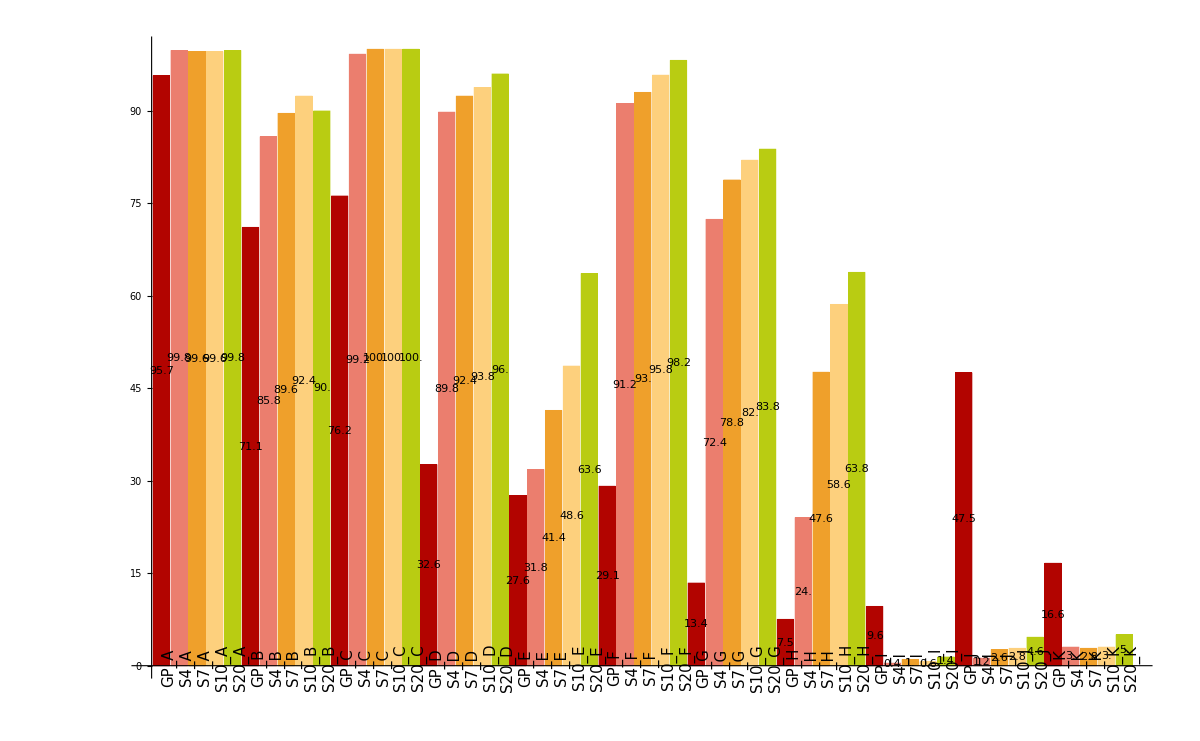

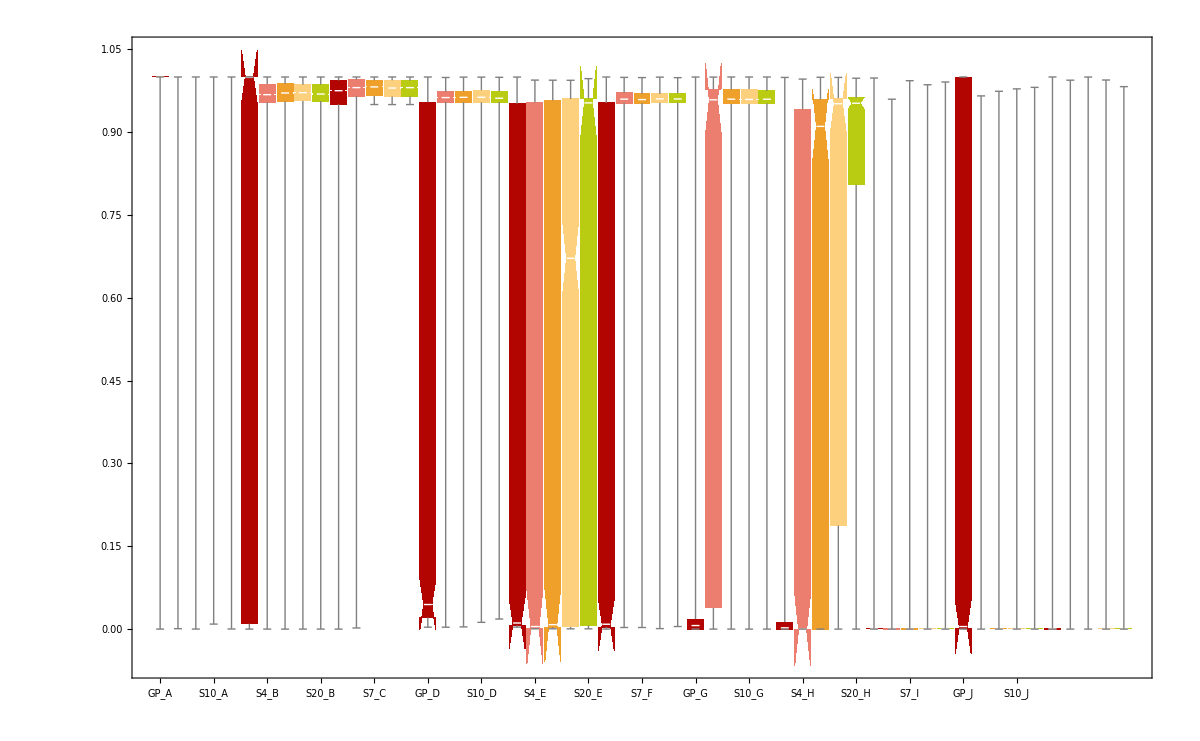
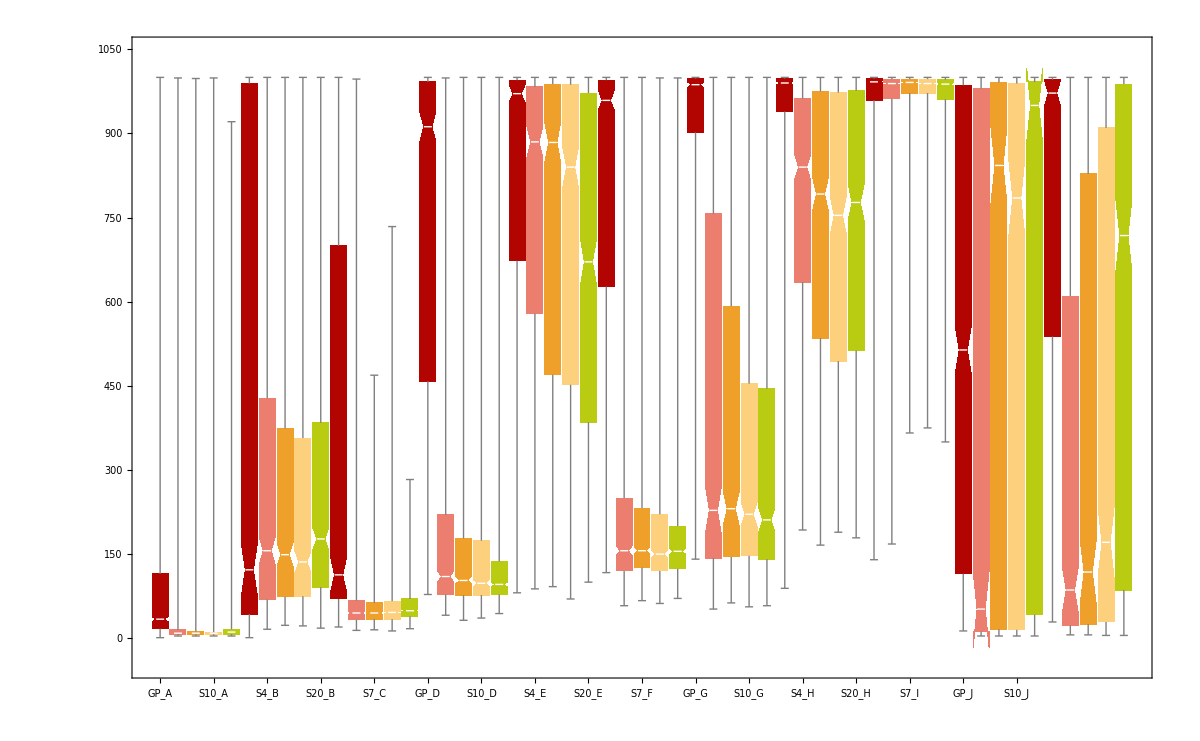
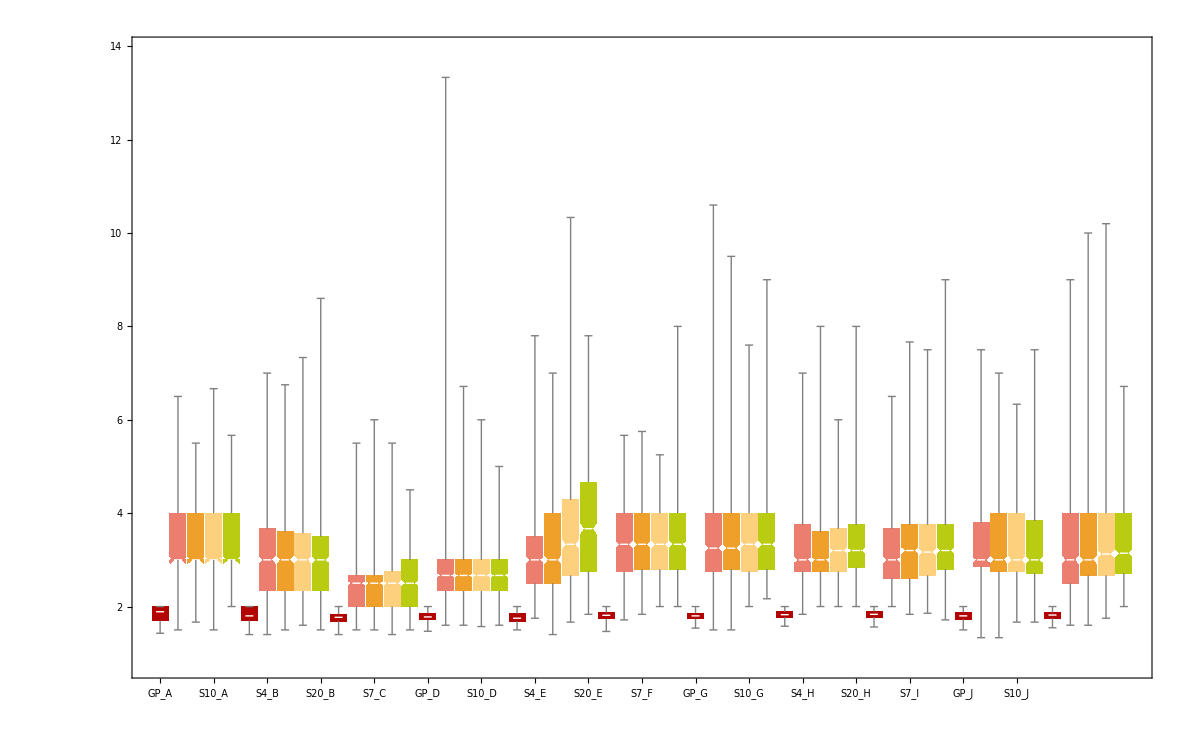
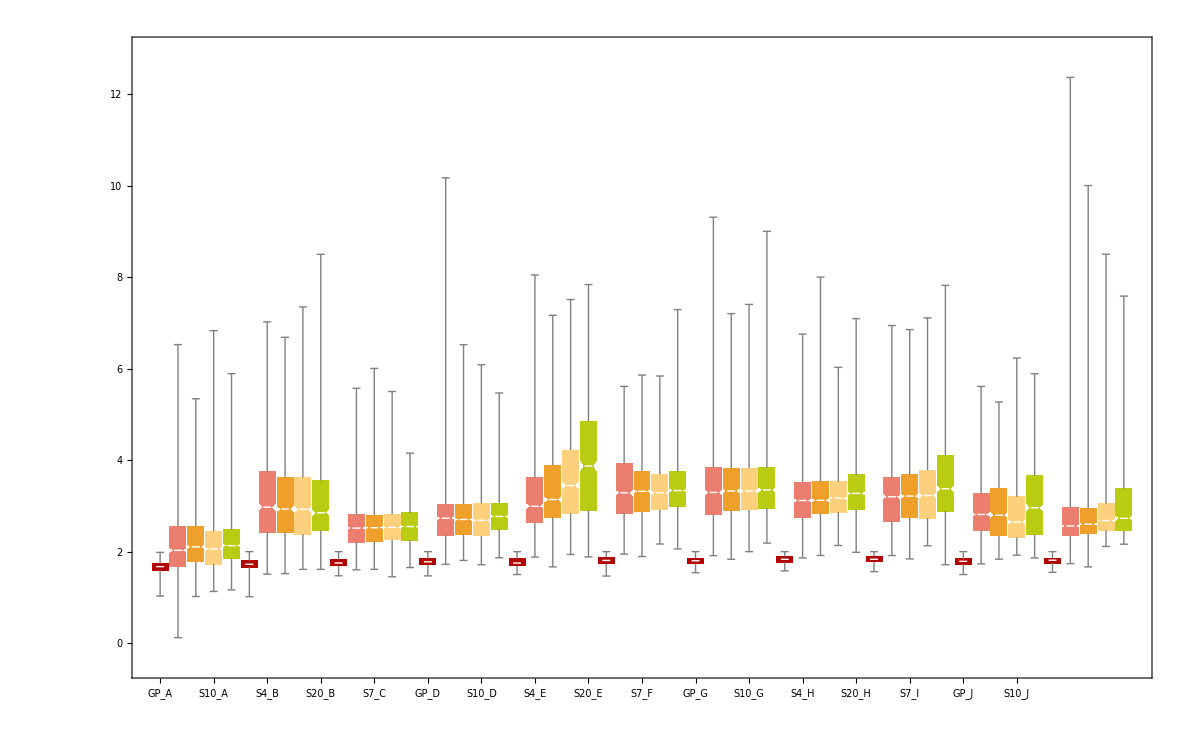
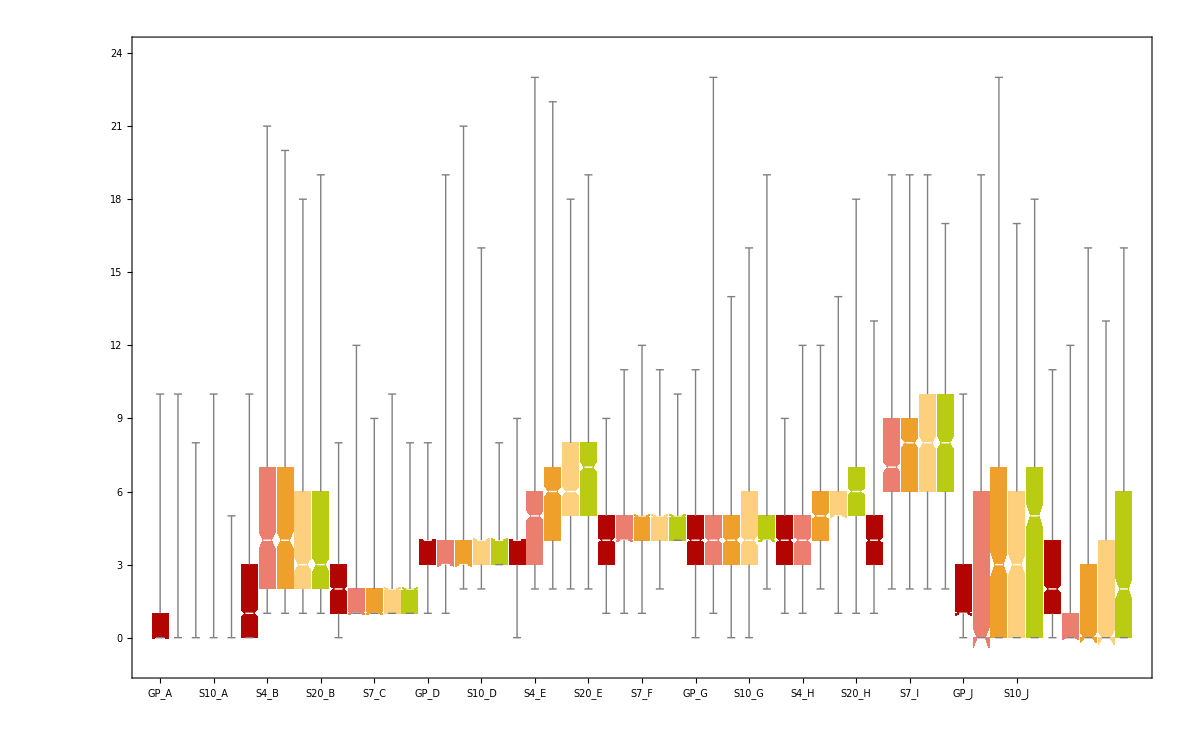
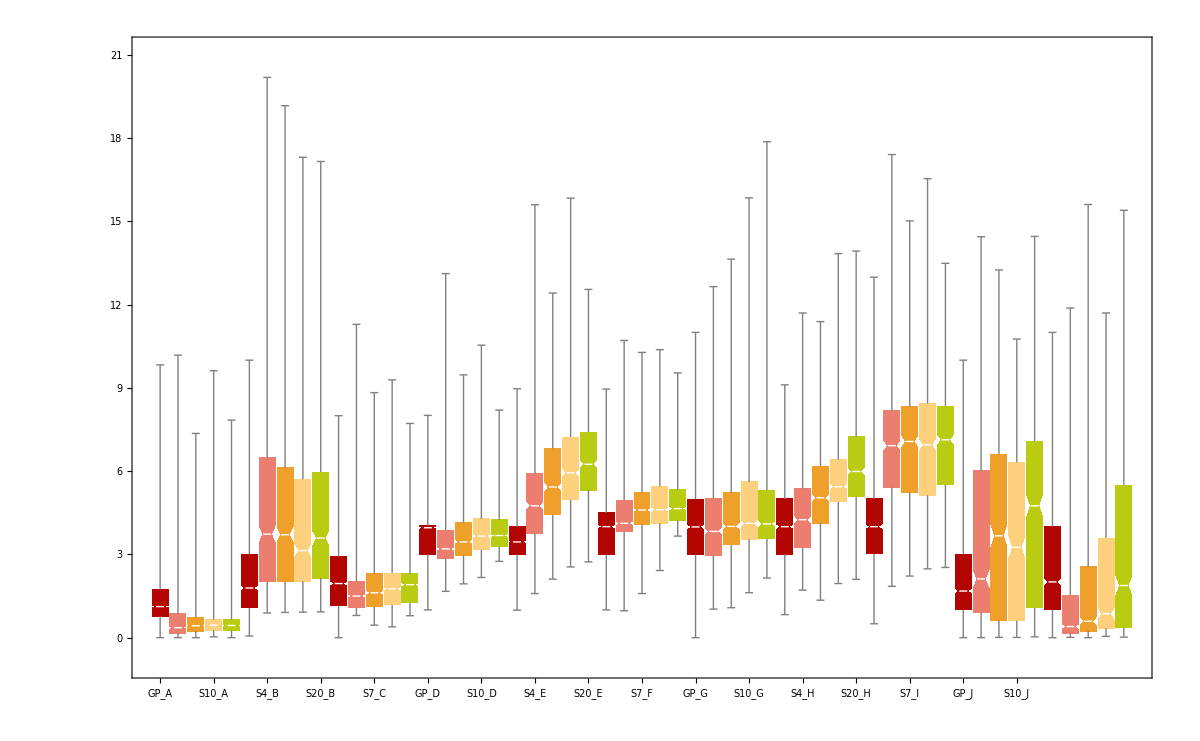
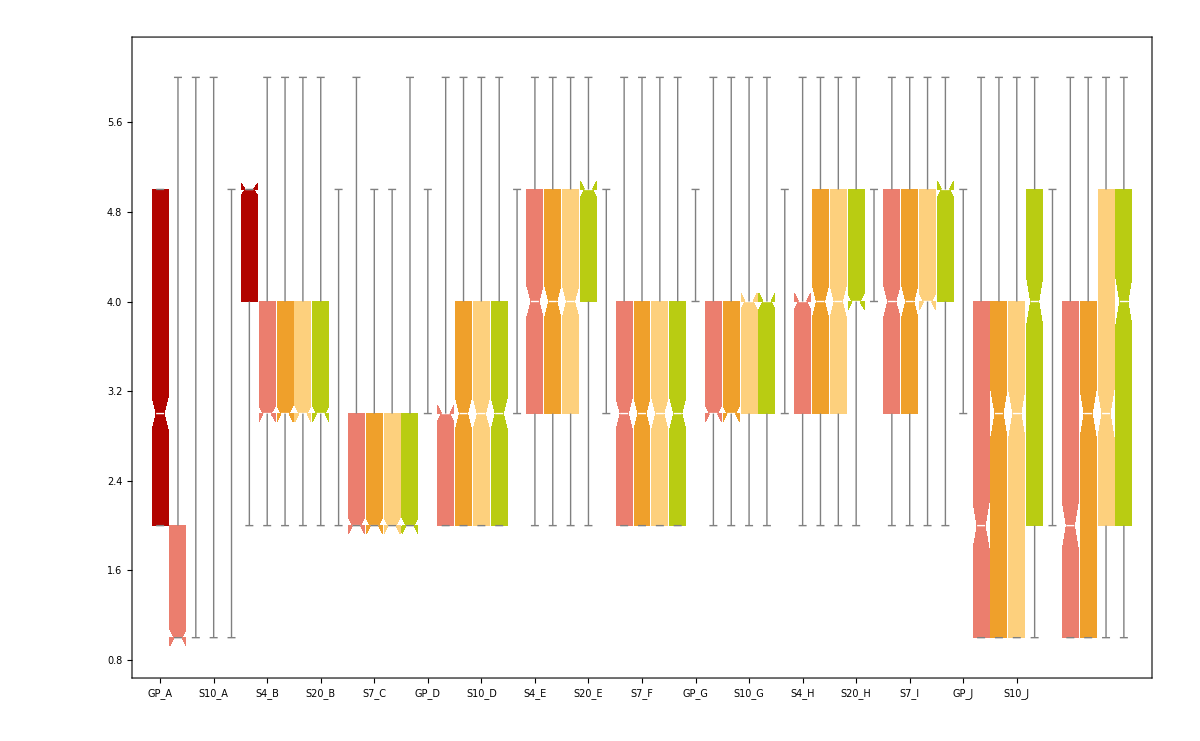
BSF | -Graphics-
BSFG | -Graphics-
ARITY_BSF | -Graphics-
ARITY_LG | -Graphics-
CONSTANTS_BSF | -Graphics-
CONSTANTS_LG | -Graphics-
DEPTH_BSF | -Graphics-
DEPTH_LG | -Graphics-
LEAVES_BSF | -Graphics-
LEAVES_LG | -Graphics-
NODES_BSF | -Graphics-
NODES_LG | -Graphics-
GENERATIONS | -Graphics-
EVALUATIONS | -Graphics-
MAX_FITNESS | -Graphics-
SUCCESS | -Graphics-
TIME | -Graphics-

```mathematica
finalStatsAll[files,labels,Null,5]
```